```mathematica
files=FileNames["*.xlsx",NotebookDirectory[]]
```

{/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/20190204.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/g1out.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/g1.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/g2.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/~$20190204.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/~$g1.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/~$g2.xlsx}

```mathematica
file = files⟦4⟧
```

/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/g2.xlsx

```mathematica
(s = Import[file])//InputForm;
```

```mathematica
s = s⟦1⟧;
```

```mathematica
data = (Interpreter["Number"][#]&/@s);
```

```mathematica
Export[FileNameJoin@{NotebookDirectory[],"g2out.xlsx"},data]
```

/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/g2out.xlsx

```mathematica
files = FileNames["*.xlsx",NotebookDirectory[]]
```

{/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/20190204.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/g1out.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/g1.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/g2out.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/g2.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/~$20190204.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/~$g1.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/~$g2out.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/~$g2.xlsx}

```mathematica
file2 = files⟦2⟧
```

/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/g1out.xlsx

```mathematica
s = Import[file2];
```

```mathematica
s =s⟦1⟧;
```

```mathematica
s
```

{{,},{0.,100000.},{2.,100000.},{4.,100000.},{6.,100000.},{8.,100000.},{10.,100000.},{12.,100000.},{14.,100000.},{16.,100000.},{18.,100000.},{20.,100000.},{22.,100000.},{24.,100000.},{26.,100000.},{28.,100000.},{30.,25631.},{32.,9951.5},{34.,5388.4},{36.,2564.1},{38.,1371.7},3019,{6078.,20.84},{6080.,20.638},{6082.,20.303},{6084.,20.075},{6086.,19.757},{6088.,19.525},{6090.,19.427},{6092.,19.195},{6094.,18.98},{6096.,18.778},{6098.,18.559},{6100.,18.447},{6102.,18.228},{6104.,18.013},{6106.,17.794},{6108.,17.665},{6110.,17.45},{6112.,17.248},{6114.,17.132},{6116.,16.93},{6118.,16.715}}
 |  |  |  |

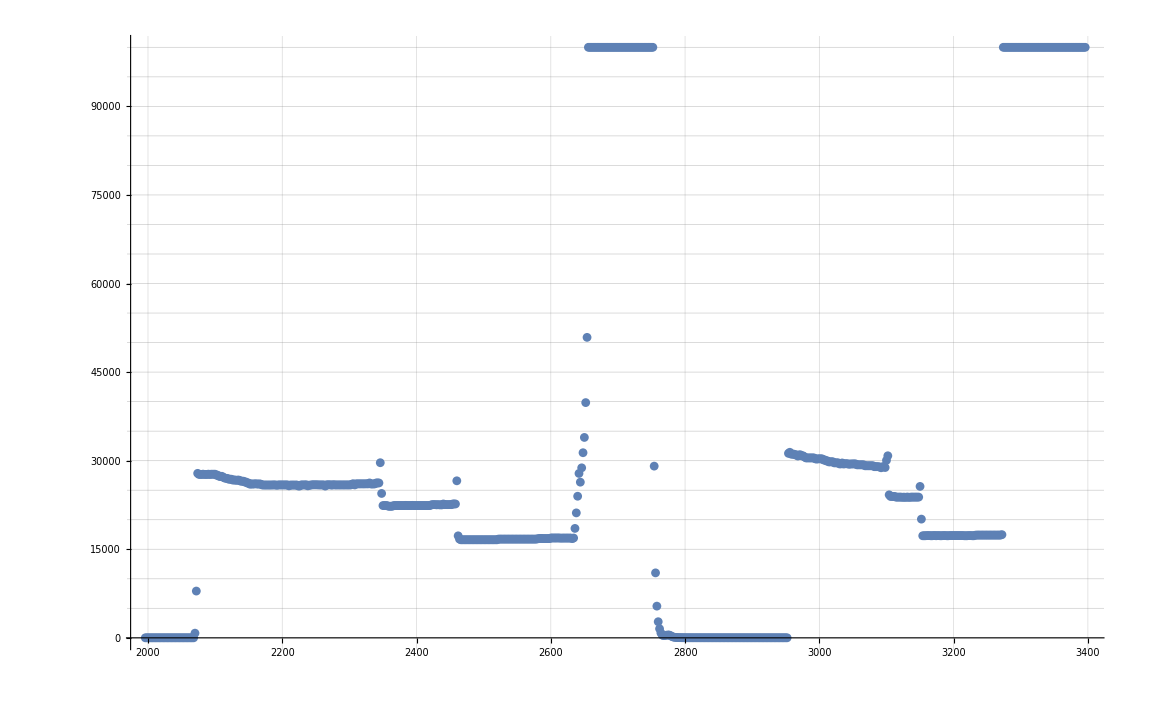

```mathematica
ListPlot[s⟦1000;;1700⟧,GridLines->{Range[0,4000,50], Range[0,100000,5000]}]
```

```mathematica
files
```

{/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/20190204.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/g1out.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/g1.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/g2out.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/g2.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/~$20190204.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/~$g1.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/~$g2out.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/~$g2.xlsx}

```mathematica
fil3 = files⟦4⟧
```

/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/g2out.xlsx

```mathematica
s = Import[fil3];
```

```mathematica
s=s⟦1⟧;
```

```mathematica
s
```

{{,},{0.,9.9×10^9},{2.,9.9×10^9},{4.,9.9×10^9},{6.,9.9×10^9},{8.,9.9×10^9},{10.,9.9×10^9},{12.,9.9×10^9},{14.,9.9×10^9},{16.,9.9×10^9},{18.,9.9×10^9},{20.,9.9×10^9},{22.,9.9×10^9},{24.,9.9×10^9},{26.,9.9×10^9},{28.,9.9×10^9},{30.,9.9×10^9},{32.,9.9×10^9},{34.,9.9×10^9},{36.,9.9×10^9},{38.,9.9×10^9},{40.,9.9×10^9},{42.,9.9×10^9},3014,{6072.,9.9×10^9},{6074.,9.9×10^9},{6076.,9.9×10^9},{6078.,9.9×10^9},{6080.,9.9×10^9},{6082.,9.9×10^9},{6084.,9.9×10^9},{6086.,9.9×10^9},{6088.,9.9×10^9},{6090.,9.9×10^9},{6092.,9.9×10^9},{6094.,9.9×10^9},{6096.,9.9×10^9},{6098.,9.9×10^9},{6100.,9.9×10^9},{6102.,9.9×10^9},{6104.,9.9×10^9},{6106.,9.9×10^9},{6108.,9.9×10^9},{6110.,9.9×10^9},{6112.,9.9×10^9},{6114.,9.9×10^9},{6116.,9.9×10^9}}
 |  |  |  |

```mathematica
line=Fit[s⟦2230;;2290⟧,{1,x},x]
```

-11.4864+0.00257531 x

```mathematica
ListPlot[s⟦2200;;2400⟧,GridLines->{Range[4000,5000,20], Range[0,0.5,0.01]}]
```

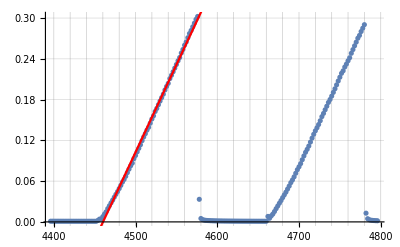

```mathematica
Show[ListPlot[s⟦2200;;2400⟧,GridLines->{Range[4000,5000,20], Range[0,0.5,0.01]}],Plot[line,{x,0,5000},PlotLegends->line,PlotStyle->Red]]
```

```mathematica
file2
```

/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/g1out.xlsx

```mathematica
(s = Import[file2])//InputForm;
```

```mathematica
s = s⟦1⟧;
```

```mathematica
s
```

{{,},{0.,100000.},{2.,100000.},{4.,100000.},{6.,100000.},{8.,100000.},{10.,100000.},{12.,100000.},{14.,100000.},{16.,100000.},{18.,100000.},{20.,100000.},{22.,100000.},{24.,100000.},{26.,100000.},{28.,100000.},{30.,25631.},{32.,9951.5},{34.,5388.4},{36.,2564.1},{38.,1371.7},3019,{6078.,20.84},{6080.,20.638},{6082.,20.303},{6084.,20.075},{6086.,19.757},{6088.,19.525},{6090.,19.427},{6092.,19.195},{6094.,18.98},{6096.,18.778},{6098.,18.559},{6100.,18.447},{6102.,18.228},{6104.,18.013},{6106.,17.794},{6108.,17.665},{6110.,17.45},{6112.,17.248},{6114.,17.132},{6116.,16.93},{6118.,16.715}}
 |  |  |  |

```mathematica
s⟦2;;All⟧
```

```mathematica
s⟦All,2⟧ = Log@s⟦All,2⟧;
```

```mathematica
s
```

{{,Log[]},{0.,11.5129},{2.,11.5129},{4.,11.5129},{6.,11.5129},{8.,11.5129},{10.,11.5129},{12.,11.5129},{14.,11.5129},{16.,11.5129},{18.,11.5129},{20.,11.5129},{22.,11.5129},3035,{6094.,2.94339},{6096.,2.93269},{6098.,2.92095},{6100.,2.9149},{6102.,2.90296},{6104.,2.89109},{6106.,2.87886},{6108.,2.87159},{6110.,2.85934},{6112.,2.8477},{6114.,2.84095},{6116.,2.82909},{6118.,2.81631}}
 |  |  |  |

```mathematica
line=Fit[s⟦50;;170⟧,{1,x},x]
```

3.15293-0.00254059 x

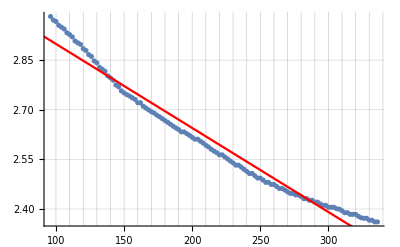

```mathematica
Show[ListPlot[s⟦50;;170⟧,GridLines->{Range[80,400,10], Range[2,4,0.05]}],Plot[line,{x,0,5000},PlotLegends->line,PlotStyle->Red]]
```

```mathematica
files
```

{/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/20190204.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/g1out.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/g1.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/g2out.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/g2.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/~$20190204.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/~$g1.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/~$g2out.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/~$g2.xlsx}

```mathematica
file = files⟦4⟧
```

/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.3.1Б/04.02.2019/g2out.xlsx

```mathematica
s = Import[file]
```

{{{,},{0.,9.9×10^9},{2.,9.9×10^9},{4.,9.9×10^9},{6.,9.9×10^9},{8.,9.9×10^9},{10.,9.9×10^9},{12.,9.9×10^9},{14.,9.9×10^9},{16.,9.9×10^9},{18.,9.9×10^9},{20.,9.9×10^9},{22.,9.9×10^9},{24.,9.9×10^9},{26.,9.9×10^9},{28.,9.9×10^9},{30.,9.9×10^9},{32.,9.9×10^9},{34.,9.9×10^9},{36.,9.9×10^9},{38.,9.9×10^9},{40.,9.9×10^9},{42.,9.9×10^9},3014,{6072.,9.9×10^9},{6074.,9.9×10^9},{6076.,9.9×10^9},{6078.,9.9×10^9},{6080.,9.9×10^9},{6082.,9.9×10^9},{6084.,9.9×10^9},{6086.,9.9×10^9},{6088.,9.9×10^9},{6090.,9.9×10^9},{6092.,9.9×10^9},{6094.,9.9×10^9},{6096.,9.9×10^9},{6098.,9.9×10^9},{6100.,9.9×10^9},{6102.,9.9×10^9},{6104.,9.9×10^9},{6106.,9.9×10^9},{6108.,9.9×10^9},{6110.,9.9×10^9},{6112.,9.9×10^9},{6114.,9.9×10^9},{6116.,9.9×10^9}}}
 |  |  |  |

```mathematica
s= s⟦1⟧;
```

```mathematica
s⟦All,2⟧ = Log@s⟦All,2⟧;
```

```mathematica
s
```

{{,Log[]},{0.,23.0158},{2.,23.0158},{4.,23.0158},{6.,23.0158},{8.,23.0158},{10.,23.0158},{12.,23.0158},{14.,23.0158},{16.,23.0158},{18.,23.0158},{20.,23.0158},{22.,23.0158},3034,{6092.,23.0158},{6094.,23.0158},{6096.,23.0158},{6098.,23.0158},{6100.,23.0158},{6102.,23.0158},{6104.,23.0158},{6106.,23.0158},{6108.,23.0158},{6110.,23.0158},{6112.,23.0158},{6114.,23.0158},{6116.,23.0158}}
 |  |  |  |

```mathematica
line=Fit[s⟦2400;;2500⟧,{1,x},x]
```

0.0146277-2.80558×10^-6 x

```mathematica
s⟦2400;;2500⟧
```

{{4796.,-6.39039},{4798.,-6.45344},{4800.,-6.50129},{4802.,-6.56197},{4804.,-6.60241},{4806.,-6.63028},{4808.,-6.66183},{4810.,-6.69007},{4812.,-6.71647},{4814.,-6.7408},{4816.,-6.76089},{4818.,-6.78607},{4820.,-6.80646},{4822.,-6.82544},{4824.,-6.83907},{4826.,-6.85327},{4828.,-6.86748},{4830.,-6.88004},{4832.,-6.89297},{4834.,-6.90366},{4836.,-6.91477},{4838.,-6.92695},{4840.,-6.93548},{4842.,-6.94468},{4844.,-6.95357},{4846.,-6.96314},{4848.,-6.97137},{4850.,-6.9805},{4852.,-6.98887},{4854.,-6.99666},{4856.,-7.00539},{4858.,-7.01117},{4860.,-7.01678},{4862.,-7.02632},{4864.,-7.03311},{4866.,-7.03951},{4868.,-7.04549},{4870.,-7.05218},{4872.,-7.05824},{4874.,-7.06276},{4876.,-7.06889},{4878.,-7.07413},{4880.,-7.07895},{4882.,-7.08495},{4884.,-7.09051},{4886.,-7.09506},{4888.,-7.10042},{4890.,-7.10292},{4892.,-7.10688},{4894.,-7.11121},{4896.,-7.11557},{4898.,-7.11812},{4900.,-7.12158},{4902.,-7.12543},{4904.,-7.12893},{4906.,-7.13224},{4908.,-7.1339},{4910.,-7.13706},{4912.,-7.14079},{4914.,-7.14264},{4916.,-7.14582},{4918.,-7.15034},{4920.,-7.15165},{4922.,-7.15354},{4924.,-7.15656},{4926.,-7.15922},{4928.,-7.16226},{4930.,-7.16627},{4932.,-7.16991},{4934.,-7.17182},{4936.,-7.17452},{4938.,-7.17781},{4940.,-7.17916},{4942.,-7.18246},{4944.,-7.18285},{4946.,-7.18421},{4948.,-7.18752},{4950.,-7.18948},{4952.,-7.18948},{4954.,-7.19163},{4956.,-7.1934},{4958.,-7.19478},{4960.,-7.19674},{4962.,-7.19813},{4964.,-7.19813},{4966.,-7.19991},{4968.,-7.20268},{4970.,-7.20268},{4972.,-7.20467},{4974.,-7.20605},{4976.,-7.20785},{4978.,-7.20925},{4980.,-7.21065},{4982.,-7.21204},{4984.,-7.21204},{4986.,-7.21405},{4988.,-7.21625},{4990.,-7.21606},{4992.,-7.21746},{4994.,-7.21746},{4996.,-7.21948}}

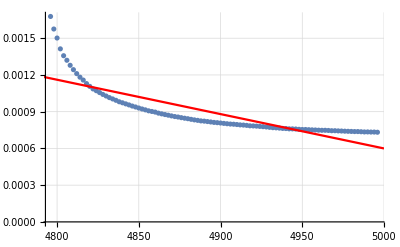

```mathematica
Show[ListPlot[s⟦2400;;2500⟧,GridLines->{Range[4000,5000,10], Range[-10,-5,0.05]}],Plot[line,{x,0,5000},PlotLegends->line,PlotStyle->Red]]
```